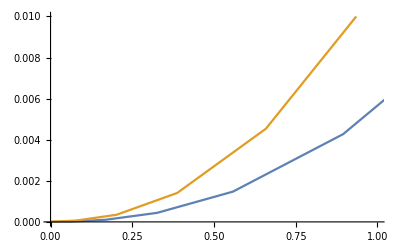

```mathematica
CumStrengths=Get[LocalObject["CumHelionStrengths"]];
dataShifted=Transpose[{#[[All,1]]-#[[All,1]][[1]],#[[All,2]]}]&/@CumStrengths;
data=dataShifted;
wgts=Flatten[Join[{Differences[data[[#]]][[All,2]][[1]],Differences[data[[#]]][[All,2]]}]]&/@Range[Length[data]];
ListPlot[data,PlotRange->{{0,1},{0,0.01}},Joined->True]
```

-CC[1]/(1.+ⅇ^((t-EE[1])/TT[1]))-CC[2]/(1.+ⅇ^((t-EE[2])/TT[2]))-CC[3]/(1.+ⅇ^((t-EE[3])/TT[3]))+CC[4]

NonlinearModelFit::acceptlev: Solved to acceptable level.

{-25771.9/(243.047+ⅇ^(0.907517 t))+25872.5/(244.904+ⅇ^(0.909091 t))-6.67699/(1.95673+ⅇ^(0.115631 t))+2.50532,-34.7633/(1.28073+ⅇ^(0.125467 t))+48.8773/(1.38214+ⅇ^(0.128296 t))-13.7364/(1.00007+ⅇ^(0.122144 t))+1.34459}

{-(96.0396 ⅇ^(0.909091 (t-6.05095)))/((1.+ⅇ^(0.909091 (t-6.05095)))^2)+(0.394572 ⅇ^(0.115631 (t-5.80529)))/((1.+ⅇ^(0.115631 (t-5.80529)))^2)+(96.2301 ⅇ^(0.907517 (t-6.05306)))/((1.+ⅇ^(0.907517 (t-6.05306)))^2),(3.40558 ⅇ^(0.125467 (t-1.97208)))/((1.+ⅇ^(0.125467 (t-1.97208)))^2)+(1.67771 ⅇ^(0.122144 (t-0.000570063)))/((1.+ⅇ^(0.122144 (t-0.000570063)))^2)-(4.53698 ⅇ^(0.128296 (t-2.52255)))/((1.+ⅇ^(0.128296 (t-2.52255)))^2)}

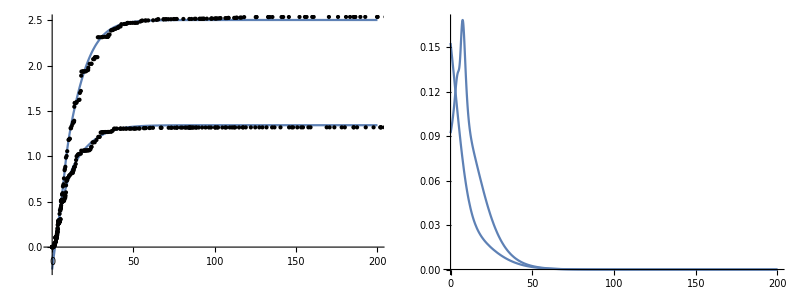

```mathematica
ClearAll;
Bdim=3;
em=2;
coffs={Array[EE,Bdim],Array[TT,Bdim],Array[CC,Bdim+1]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{0.2,0.8},Length[Flatten[coffs]]]}];
constrEE=10.3^em>#>0&/@coffs[[1]];
constrTT=10.3^em>#>1.1&/@coffs[[2]];
constrCC=10.3^em>#&/@coffs[[3]];
constr=Union[constrEE,constrTT,constrCC];
FermiModel=coffs[[3]][[Bdim+1]]-Sum[coffs[[3]][[n]]/(1.+Exp[(t-coffs[[1]][[n]])/coffs[[2]][[n]]]),{n,Bdim}]
fitRangeMin=10;fitRangeMax=301;
SetSharedVariable[sols]
sols={};

ParallelDo[
optPOSsol=
NonlinearModelFit[dataShifted[[nn]][[fitRangeMin;;fitRangeMax]],{FermiModel,constr},inicoffs,t,Weights->wgts[[nn]][[fitRangeMin;;fitRangeMax]],MaxIterations->2500,AccuracyGoal->10];
AppendTo[sols,optPOSsol[t]];
,{nn,Range[Length[dataShifted]]}]
cums=Simplify[#]&/@sols;
resps=D[#,t]&/@sols;
cums//TraditionalForm
resps//TraditionalForm
Emax=200;
Grid[{{
Plot[cums[[#]]/.t->tt&/@Range[Length[data]],{tt,0,Emax},Epilog->{PointSize[Small],Point[#]&/@data},PlotRange->{{-1,Emax},Automatic},ImageSize->500],
Plot[resps[[#]]/.t->tt&/@Range[Length[data]],{tt,0,Emax},PlotRange->Full,ImageSize->500]
}}]
```